```mathematica
Brake1[t_,τ_,βr_]:=βr/2*(Tanh[20t]-Tanh[20(t-τ)])
(* The following version of Brake[] implements an automatic reaction of the braeaking system if a limit is excieded. The version did not work properly because I may not correctly use the parameters for the break. Adapt it so that it works at the proper time t in the system of equations. *)
```

```mathematica
Brake[t_,τ0_,τ_,βr_]:=Block[{τ01,τ1,β1},
Piecewise[{{τ01={t};τ1={t+2};β1={1.};Fold[Plus,0,Table[Brake1[t-τ01⟦k⟧,τ1⟦k⟧,β1⟦k⟧],{k,1,Length[τ1]}]],Subscript[e, y][t] > 200},{Fold[Plus,0,Table[Brake1[t-τ0⟦k⟧,τ⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]],Subscript[e, y][t] ≤ 200}}]]
```

```mathematica
Brake[t_,τ0_,τ_,βr_]:=
Fold[Plus,0,Table[Brake1[t-τ0⟦k⟧,τ⟦k⟧,βr⟦k⟧],{k,1,Length[τ]}]];
```

```mathematica
(* there was a problem in your definition of Subscript[β, r]. I replaced it by a unique symbol βr. Mathematica hase sometimes problems with indexed variables like your Subscript[β, r]. Good practice is to avoid all indexed variables in subscript notation. *)

τ0 = {1,10,20,50};
τ = {0.6,3,5,5};
β={0,0,0,.0};
βr= Brake[t,τ0 ,τ ,β];
η = √(1.0-βr^2);
```

```mathematica
(* the path must be adjusted on your computer *)

q= Import["1.dat"];
q1 = DeleteCases[Table[If[q[[k,1]] == q[[k+1,1]], null ,q[[k+1]]],{k,1,Length[q]-1}],null];
q2 = Map[({First[#]-0.2945,Last[#]})&,q1];
q3 = Interpolation[q2];
δ= δ(*(q3[t])*);
```

```mathematica
rules =
{
C1->80000.0,C2->80000.0,C3->80000.0,C4->80000.0,
μ1->1.0,μ2->1.0,μ3->1.0,μ4->1.0,
Fz1->26719.0,Fz2->26719.0,Fz3->21295.0,Fz4->21295.0(*NOT SURE*),
m ->2050.0,Subscript[ω, t]->1.63,Subscript[l, f]->1.43,Subscript[l, r]->1.47 , Subscript[J, z] -> 3344.0 ,
Subscript[K, y]->5000,Subscript[K, ψ]-> 0,Subscript[ψ, d1] ->-0.12,Subscript[t, lp] -> 1.5
};
```

```mathematica
(* Slip angle *) 
f1[μ_,F_,C_]:=ArcTan[(3η μ F)/C]/.rules;
Subscript[α, sl1]=f1[μ1,Fz1,C1]; Subscript[α, sl2]=f1[μ2,Fz2,C2];
Subscript[α, sl3]=f1[μ3,Fz3,C3]; Subscript[α, sl4]=f1[μ4,Fz4,C4];

f2[δ_,l_]:=(y'[t] + l ψ'[t])/x'[t]-δ/.rules;
α1=f2[δ,Subscript[l, f]]; Subscript[α, 2]=f2[δ,Subscript[l, f]];
Subscript[α, 3]=f2[0,-Subscript[l, r]]; Subscript[α, 4]=f2[0,-Subscript[l, r]];
```

```mathematica
(* Tire  Lateral Force *)
f3[C_,α_,μ_,F_,αs_]:=Piecewise[{{- C Tan[α]+ C^2/(3η μ F) Abs[Tan[α]] Tan[α]- C^3/(27(η μ F)^2)Tan[α]^3, Abs[α]<αs}, {-η μ F Sign[α], Abs[α]≥αs}}];
Subscript[f, y1]=f3[C1,α1,μ1,Fz1,Subscript[α, sl1]]/.rules; Subscript[f, y2]=f3[C2,Subscript[α, 2],μ2,Fz2,Subscript[α, sl2]]/.rules;
Subscript[f, y3]=f3[C3,Subscript[α, 3],μ3,Fz3,Subscript[α, sl3]]/.rules; Subscript[f, y4]=f3[C4,Subscript[α, 4],μ4,Fz4,Subscript[α, sl4]]/.rules;
```

```mathematica
(* Tire  Longitudinal Force *) 
f4[μ_,F_]:=βr μ F/.rules;
Subscript[f, x1]=f4[μ1,Fz1]/.rules; Subscript[f, x2]=f4[μ2,Fz2]/.rules;
Subscript[f, x3]=f4[μ3,Fz3]/.rules; Subscript[f, x4]=f4[μ4,Fz4]/.rules;
```

```mathematica
(* Long. and Lat. Tot. Forces *)
Subscript[F, x1] =Subscript[f, x1] Cos[δ] - Subscript[f, y1] Sin[δ]; Subscript[F, x2] =Subscript[f, x2] Cos[δ] - Subscript[f, y2] Sin[δ];
Subscript[F, x3] =Subscript[f, x3] Cos[0] - Subscript[f, y3] Sin[0]; Subscript[F, x4] =Subscript[f, x4] Cos[0] - Subscript[f, y4] Sin[0];

Subscript[F, y1] =Subscript[f, x1] Sin[δ] + Subscript[f, y1] Cos[δ]; Subscript[F, y2] =Subscript[f, x2] Sin[δ] + Subscript[f, y2] Cos[δ];
Subscript[F, y3] =Subscript[f, x3] Sin[0] + Subscript[f, y3] Cos[0]; Subscript[F, y4] =Subscript[f, x4] Sin[0] + Subscript[f, y4] Cos[0];
```

```mathematica
(*phi = (0) + (Subscript[Ce, 0]*x[t]) +(1/2 Subscript[Ce, 1]*(x[t])^2)
u = (0) + phi*x[t] + (1/2 Subscript[Ce, 0]*(x[t])^2) + (1/6 Subscript[Ce, 1]*(x[t])^3);*)
u[t_] :=  0.0001 t^2+0.5;
(* Equations of Motion *)
Eq1 = m x''[t]== m y'[t]ψ'[t] + Subscript[F, x1] +Subscript[F, x2] +Subscript[F, x3] +Subscript[F, x4];
Eq2 = m y''[t] == -m x'[t] ψ'[t] + Subscript[F, y1]+ Subscript[F, y2]+ Subscript[F, y3]+ Subscript[F, y4];
Eq3 =Subscript[J, z] ψ''[t] == Subscript[l, f](Subscript[F, y1] + Subscript[F, y2]) - Subscript[l, r](Subscript[F, y3] + Subscript[F, y4]) + (Subscript[ω, t]/2)( Subscript[F, x2] -Subscript[F, x1] - Subscript[F, x3] + Subscript[F, x4]);
Eq4 = Subscript[e, ψ]'[t]==( ψ'[t]-u''[t]);
Eq5 = Subscript[e, y]'[t]==(*ψ'[t]-0.0002 t*)y'[t] Cos[Subscript[e, ψ][t]] + x'[t]Sin[Subscript[e, ψ][t]];
```

```mathematica
motionEq ={Eq1,Eq2,Eq3,Eq4,Eq5}/.rules
```

{2050. x''[t]==0.-2 (Piecewise[{{80000. Tan[δ-(y'[t]+1.43 ψ'[t])/x'[t]]-79843.3 Abs[Tan[δ-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[δ-(y'[t]+1.43 ψ'[t])/x'[t]]+26562.3 Tan[δ-(y'[t]+1.43 ψ'[t])/x'[t]]^3, Abs[-δ+(y'[t]+1.43 ψ'[t])/x'[t]]<0.786378}, {-26719. Sign[-δ+(y'[t]+1.43 ψ'[t])/x'[t]], Abs[-δ+(y'[t]+1.43 ψ'[t])/x'[t]]≥0.786378}, {0, True}}]) Sin[δ]+2050. y'[t] ψ'[t],2050. y''[t]==0.+2 (Piecewise[{{-80000. Tan[(y'[t]-1.47 ψ'[t])/x'[t]]+100180. Abs[Tan[(y'[t]-1.47 ψ'[t])/x'[t]]] Tan[(y'[t]-1.47 ψ'[t])/x'[t]]-41816.8 Tan[(y'[t]-1.47 ψ'[t])/x'[t]]^3, Abs[(y'[t]-1.47 ψ'[t])/x'[t]]<0.673864}, {-(21295. Sign[y'[t]-1.47 ψ'[t]])/Sign[x'[t]], Abs[(y'[t]-1.47 ψ'[t])/x'[t]]≥0.673864}, {0, True}}])+2 Cos[δ] (Piecewise[{{80000. Tan[δ-(y'[t]+1.43 ψ'[t])/x'[t]]-79843.3 Abs[Tan[δ-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[δ-(y'[t]+1.43 ψ'[t])/x'[t]]+26562.3 Tan[δ-(y'[t]+1.43 ψ'[t])/x'[t]]^3, Abs[-δ+(y'[t]+1.43 ψ'[t])/x'[t]]<0.786378}, {-26719. Sign[-δ+(y'[t]+1.43 ψ'[t])/x'[t]], Abs[-δ+(y'[t]+1.43 ψ'[t])/x'[t]]≥0.786378}, {0, True}}])-2050. x'[t] ψ'[t],3344. ψ''[t]==0.-1.47 (0.+2 (Piecewise[{{-80000. Tan[(y'[t]-1.47 ψ'[t])/x'[t]]+100180. Abs[Tan[(y'[t]-1.47 ψ'[t])/x'[t]]] Tan[(y'[t]-1.47 ψ'[t])/x'[t]]-41816.8 Tan[(y'[t]-1.47 ψ'[t])/x'[t]]^3, Abs[(y'[t]-1.47 ψ'[t])/x'[t]]<0.673864}, {-(21295. Sign[y'[t]-1.47 ψ'[t]])/Sign[x'[t]], Abs[(y'[t]-1.47 ψ'[t])/x'[t]]≥0.673864}, {0, True}}]))+1.43 (0.+2 Cos[δ] (Piecewise[{{80000. Tan[δ-(y'[t]+1.43 ψ'[t])/x'[t]]-79843.3 Abs[Tan[δ-(y'[t]+1.43 ψ'[t])/x'[t]]] Tan[δ-(y'[t]+1.43 ψ'[t])/x'[t]]+26562.3 Tan[δ-(y'[t]+1.43 ψ'[t])/x'[t]]^3, Abs[-δ+(y'[t]+1.43 ψ'[t])/x'[t]]<0.786378}, {-26719. Sign[-δ+(y'[t]+1.43 ψ'[t])/x'[t]], Abs[-δ+(y'[t]+1.43 ψ'[t])/x'[t]]≥0.786378}, {0, True}}])),e_ψ'[t]==-0.0002+ψ'[t],e_y'[t]==Sin[e_ψ[t]] x'[t]+Cos[e_ψ[t]] y'[t]}

```mathematica
time =70;
initCond={x[0]==0.1,x'[0]==10,y[0]==0.0,y'[0]==0.00,ψ[0]==0.00,ψ'[0]==0, Subscript[e, ψ][0] == 00.05, Subscript[e, y][0] == -1};
solution=NDSolve[Flatten[{motionEq/.rules,initCond}],{x,y,ψ,Subscript[e, ψ],Subscript[e, y]},{t,0,time}];
```

## The Ruler Allignment versus Democratic Mutually Synchronized Allignment (Driver)

Currently the ruler model is implemented by soley dictating the use of the steering wheel by the algorithm. The optimal allignment of the car to the ideal line of the road is done in two steps an optimization step and a solution step. The total motion of the car is therefore split up in n subintervals in which an allignment to the ideal line of the road is performed. After determining the optimal steering angle during this period the actual motion of the car using the optimal steering angle is calculated. According to the two steps we define two functions performing the needed steps. The first one costFunction2[] is used in the optimization. The second one costFunction1[] delivers the numerical solution. The two functions are used in the calculation of the optimal path in the governing function optimalPath[].

```mathematica
costFunction1[δ1_?NumericQ,{tstart_,tend_},initialValues_,idealRoad_]:=Block[{motionEq,time,initCond,solution,points,pl1,ΔxVec,lineElement,initVars,vars,velocity,tangent,cosθ},
(* --- the ideal line of the car is given as a polynomial --- *)
pl1=idealRoad;
(* equations of motion *)
motionEq ={Eq1,Eq2,Eq3,Eq4,Eq5}/.rules/.δ->δ1;
(* generate initial conditions *)
vars={x[t],x'[t],y[t],y'[t],ψ[t],ψ'[t],Subscript[e, ψ][t],Subscript[e, y][t]};
initVars=vars/.t->tstart;
initCond=Thread[initVars==initialValues];
(* solve the equations of motion *)
    solution=NDSolve[Flatten[{motionEq/.rules,initCond}],{x,y,ψ,Subscript[e, ψ],Subscript[e, y]},{t,tstart,tend}];
(* determine the vector for the line element *)
ΔxVec={x[t]-(x/.Flatten[Solve[y[t]==pl1,x]]),(pl1/.x->x[t])-y[t]};
(* calculate the line element at the endpoint of the interval *)
lineElement=ΔxVec/.Flatten[solution]/.t->tend;
(* determine the velocity vector *)
velocity={x'[t],y'[t]}/.Flatten[solution]/.t->tend;
(* calculate the tangent vector to the ideal line of the road *)
tangent={1,D[pl1, x]}/.x->x[t]/.Flatten[solution]/.t->tend;
(* the cos of the angle between velocity and tangent line of the road *)
cosθ=(tangent.velocity)/(Norm[tangent] Norm[velocity]);
(* return the different values and the solution as well as the initial conditions for the next step *)
{√(lineElement.Conjugate[lineElement]),1-cosθ,solution,(vars/.Flatten[solution]/.t->tend)}
]
```

```mathematica
costFunction2[δ1_?NumericQ,{tstart_,tend_},initialValues_,idealRoad_]:=Block[{motionEq,time,initCond,solution,points,pl1,ΔxVec,lineElement,initVars,vars,velocity,tangent,cosθ},
(* --- the ideal line of the car is given as a polynomial --- *)
pl1=idealRoad;
(* equations of motion *)
motionEq ={Eq1,Eq2,Eq3,Eq4,Eq5}/.rules/.δ->δ1;
(* generate initial conditions *)
vars={x[t],x'[t],y[t],y'[t],ψ[t],ψ'[t],Subscript[e, ψ][t],Subscript[e, y][t]};
initVars=vars/.t->tstart;
initCond=Thread[initVars==initialValues];
(* solve the equations of motion *)
    solution=NDSolve[Flatten[{motionEq/.rules,initCond}],{x,y,ψ,Subscript[e, ψ],Subscript[e, y]},{t,tstart,tend}];
(* determine the vector for the line element *)
ΔxVec={x[t]-(x/.Flatten[Solve[y[t]==pl1,x]]),(pl1/.x->x[t])-y[t]};
(* calculate the line element at the endpoint of the interval *)
lineElement=ΔxVec/.Flatten[solution]/.t->tend;
(* determine the velocity vector *)
velocity={x'[t],y'[t]}/.Flatten[solution]/.t->tend;
(* calculate the tangent vector to the ideal line of the road *)
tangent={1,D[pl1, x]}/.x->x[t]/.Flatten[solution]/.t->tend;
(* the cos of the angle between velocity and tangent line of the road *)
cosθ=(tangent.velocity)/(Norm[tangent] Norm[velocity]);
(* here follows the cost function *)
(√(lineElement.Conjugate[lineElement]))^2+(1-cosθ)^2
]
```

```mathematica
optimalPath[initialVals_,idealRoad_,{tstart_,tend_},numberOfDivisions_]:=Block[{δt,initVal,minval,δ1,ts,te,cf1,counter,solutions={}},
(* --- fix time step --- *)
δt=(tend-tstart)/numberOfDivisions;
initVal=initialVals;
ts=tstart;
te=ts+δt;
counter=0;
(* -- loop over the time interval -- *)
While[counter<numberOfDivisions,
Print["--- Minimum search --- "];
(* -- find optimal parameters -- *)
minval=FindMinimum[costFunction2[δ,{ts,te},initVal,idealRoad],δ];
Print["minval = {min,δ} = ",minval];
(* --- use optimal parametsrs for the solution --- *)
δ1=δ/.Last[minval];
cf1=costFunction1[δ1,{ts,te},initVal,idealRoad];
(* --- collect the solutions --- *)
AppendTo[solutions,{{ts,te},cf1⟦3⟧,δ1}];
(* --- update the initial conditions --- *)
initVal=Last[cf1];
ts=te;
te=te+δt;
counter=counter+1;
];
solutions
]
```

```mathematica
initVals={.1,10,-1.,1.00,0.00,0,00.05,-1}
```

{0.1,10,-1.,1.,0.,0,0.05,-1}

```mathematica
points={{0,0},{700,-40}};
idealLineRoad=InterpolatingPolynomial[points,x]//Expand
```

-(2 x)/35

```mathematica
sols=optimalPath[initVals,idealLineRoad,{0,3.5},50];
```

--- Minimum search ---

minval = {min,δ} = {228.892,{δ→0.692254}}

--- Minimum search ---

minval = {min,δ} = {153.069,{δ→0.862289}}

--- Minimum search ---

minval = {min,δ} = {87.3408,{δ→0.97707}}

--- Minimum search ---

minval = {min,δ} = {37.6684,{δ→1.06296}}

--- Minimum search ---

minval = {min,δ} = {7.91876,{δ→1.13233}}

--- Minimum search ---

minval = {min,δ} = {0.00244799,{δ→0.587336}}

--- Minimum search ---

minval = {min,δ} = {1.74251,{δ→-0.345273}}

--- Minimum search ---

minval = {min,δ} = {0.317329,{δ→3.05642}}

--- Minimum search ---

minval = {min,δ} = {0.00807092,{δ→0.257917}}

--- Minimum search ---

minval = {min,δ} = {2.43145×10^-7,{δ→1.72705}}

--- Minimum search ---

minval = {min,δ} = {5.04312×10^-6,{δ→1.40465}}

--- Minimum search ---

minval = {min,δ} = {0.0721149,{δ→1.56857}}

--- Minimum search ---

minval = {min,δ} = {0.00707846,{δ→-0.390029}}

--- Minimum search ---

minval = {min,δ} = {0.00644084,{δ→-0.436435}}

--- Minimum search ---

minval = {min,δ} = {0.00576602,{δ→-0.431359}}

--- Minimum search ---

minval = {min,δ} = {0.005138,{δ→-0.425276}}

--- Minimum search ---

minval = {min,δ} = {0.00455682,{δ→-0.419048}}

--- Minimum search ---

minval = {min,δ} = {0.0040208,{δ→-0.412682}}

--- Minimum search ---

minval = {min,δ} = {0.0035282,{δ→-0.40617}}

--- Minimum search ---

minval = {min,δ} = {0.00307725,{δ→-0.399502}}

--- Minimum search ---

minval = {min,δ} = {0.00254669,{δ→-14.2741}}

--- Minimum search ---

minval = {min,δ} = {0.0374931,{δ→1.26487}}

--- Minimum search ---

minval = {min,δ} = {0.000532413,{δ→-0.447448}}

--- Minimum search ---

minval = {min,δ} = {2.88355×10^-6,{δ→-0.22758}}

--- Minimum search ---

minval = {min,δ} = {2.10829×10^-15,{δ→-0.112161}}

--- Minimum search ---

minval = {min,δ} = {1.21948×10^-18,{δ→-0.112774}}

--- Minimum search ---

minval = {min,δ} = {4.33599×10^-18,{δ→-0.11276}}

--- Minimum search ---

minval = {min,δ} = {1.23172×10^-18,{δ→-0.112761}}

--- Minimum search ---

minval = {min,δ} = {1.22187×10^-18,{δ→-0.112761}}

--- Minimum search ---

minval = {min,δ} = {1.23414×10^-18,{δ→-0.112761}}

--- Minimum search ---

minval = {min,δ} = {4.45443×10^-18,{δ→-0.112761}}

--- Minimum search ---

minval = {min,δ} = {1.2435×10^-18,{δ→-0.112761}}

--- Minimum search ---

minval = {min,δ} = {0.0218442,{δ→0.901312}}

--- Minimum search ---

minval = {min,δ} = {0.0052578,{δ→-0.526298}}

--- Minimum search ---

minval = {min,δ} = {0.00229023,{δ→-0.551363}}

--- Minimum search ---

minval = {min,δ} = {0.00060098,{δ→-0.457118}}

--- Minimum search ---

minval = {min,δ} = {0.0000646277,{δ→-0.333757}}

--- Minimum search ---

minval = {min,δ} = {5.40694×10^-7,{δ→-0.187334}}

--- Minimum search ---

minval = {min,δ} = {4.91142×10^-13,{δ→-0.11508}}

--- Minimum search ---

minval = {min,δ} = {2.31107×10^-19,{δ→-0.112713}}

--- Minimum search ---

minval = {min,δ} = {1.02839×10^-19,{δ→-0.112737}}

--- Minimum search ---

minval = {min,δ} = {9.59453×10^-20,{δ→-0.112736}}

--- Minimum search ---

minval = {min,δ} = {2.24215×10^-19,{δ→-0.112736}}

--- Minimum search ---

minval = {min,δ} = {1.0564×10^-19,{δ→-0.112736}}

--- Minimum search ---

minval = {min,δ} = {1.02029×10^-19,{δ→-0.112736}}

--- Minimum search ---

minval = {min,δ} = {1.06392×10^-19,{δ→-0.112736}}

--- Minimum search ---

minval = {min,δ} = {2.24201×10^-19,{δ→-0.112736}}

--- Minimum search ---

minval = {min,δ} = {2.267×10^-19,{δ→-0.112736}}

--- Minimum search ---

minval = {min,δ} = {9.84576×10^-20,{δ→-0.112736}}

--- Minimum search ---

minval = {min,δ} = {1.05545×10^-19,{δ→-0.112736}}

```mathematica
plots=Map[Apply[ParametricPlot,{{x[t],y[t]}/.Flatten[#⟦2⟧],Prepend[First[#],t]}]&,sols];
```

```mathematica
stearingAngle=Map[{Mean[First[#]],Last[#]}&,sols]
```

{{0.035,0.692254},{0.105,0.862289},{0.175,0.97707},{0.245,1.06296},{0.315,1.13233},{0.385,0.587336},{0.455,-0.345273},{0.525,3.05642},{0.595,0.257917},{0.665,1.72705},{0.735,1.40465},{0.805,1.56857},{0.875,-0.390029},{0.945,-0.436435},{1.015,-0.431359},{1.085,-0.425276},{1.155,-0.419048},{1.225,-0.412682},{1.295,-0.40617},{1.365,-0.399502},{1.435,-14.2741},{1.505,1.26487},{1.575,-0.447448},{1.645,-0.22758},{1.715,-0.112161},{1.785,-0.112774},{1.855,-0.11276},{1.925,-0.112761},{1.995,-0.112761},{2.065,-0.112761},{2.135,-0.112761},{2.205,-0.112761},{2.275,0.901312},{2.345,-0.526298},{2.415,-0.551363},{2.485,-0.457118},{2.555,-0.333757},{2.625,-0.187334},{2.695,-0.11508},{2.765,-0.112713},{2.835,-0.112737},{2.905,-0.112736},{2.975,-0.112736},{3.045,-0.112736},{3.115,-0.112736},{3.185,-0.112736},{3.255,-0.112736},{3.325,-0.112736},{3.395,-0.112736},{3.465,-0.112736}}

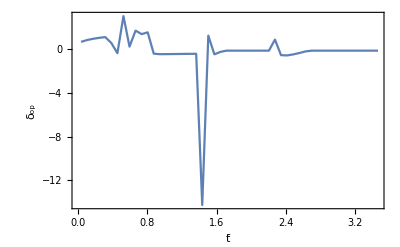

```mathematica
ListPlot[stearingAngle,Joined->True,InterpolationOrder->1,PlotRange->All,Frame->True,FrameLabel->{"t̄","δ_op"}]
```

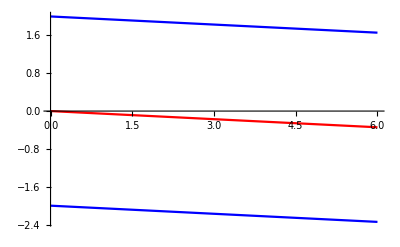

```mathematica
pl0=Plot[{idealLineRoad,idealLineRoad+2,idealLineRoad-2},{x,0,6},PlotStyle->{Red,Blue,Blue}]
```

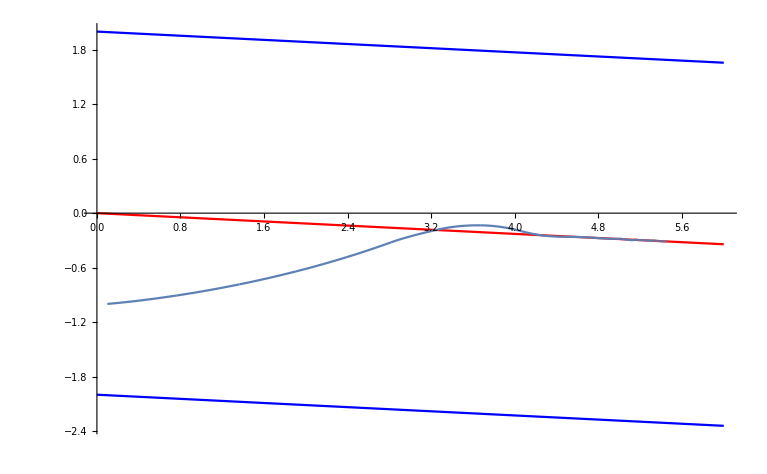

```mathematica
Show[{pl0,plots},PlotRange->All]
```

```mathematica
Plot[Evaluate[costFunction1[δ,{0,.1},initVals]],{δ,-2,2}]
```

$Aborted

```mathematica
FindMinimum[costFunction2[δ,{0,.1},initVals],δ]
```

{1.06099,{δ→0.795223}}

```mathematica
cf1=costFunction1[0.7952226894895003,{0,.1},initVals]
```

{1.03004,0.00186293,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{2.01764,8.48589,0.142436,1.74194,0.0872342,1.49947,0.137214,-0.784905}}

```mathematica
FindMinimum[costFunction2[δ,{0.1,.2},Last[cf1]],δ]
```

{0.180945,{δ→1.02581}}

```mathematica
cf2=costFunction1[1.0258091766067452,{.1,.2},Last[cf1]]
```

{0.425205,0.0120827,{{x→InterpolatingFunction[{{0.1, 0.2}}, <>],y→InterpolatingFunction[{{0.1, 0.2}}, <>],ψ→InterpolatingFunction[{{0.1, 0.2}}, <>],e_ψ→InterpolatingFunction[{{0.1, 0.2}}, <>],e_y→InterpolatingFunction[{{0.1, 0.2}}, <>]}},{2.78402,6.96277,0.336895,2.12974,0.264396,1.94599,0.314356,-0.429207}}

```mathematica
FindMinimum[costFunction2[δ,{0.2,.3},Last[cf2]],δ]
```

{1.23289×10^-6,{δ→0.483591}}

```mathematica
cf3=costFunction1[0.48359112417131966,{.2,.3},Last[cf2]]
```

{0.0000147245,0.00111026,{{x→InterpolatingFunction[{{0.2, 0.3}}, <>],y→InterpolatingFunction[{{0.2, 0.3}}, <>],ψ→InterpolatingFunction[{{0.2, 0.3}}, <>],e_ψ→InterpolatingFunction[{{0.2, 0.3}}, <>],e_y→InterpolatingFunction[{{0.2, 0.3}}, <>]}},{3.50628,7.31864,0.49939,1.39373,0.412677,1.26981,0.462617,-0.00179581}}

```mathematica
FindMinimum[costFunction2[δ,{0.4,.5},Last[cf3]],δ]
```

{4.32721×10^-8,{δ→0.308035}}

```mathematica
cf4=costFunction1[0.3080344135303448,{.3,.4},Last[cf3]]
```

{8.81182×10^-7,0.000208018,{{x→InterpolatingFunction[{{0.3, 0.4}}, <>],y→InterpolatingFunction[{{0.3, 0.4}}, <>],ψ→InterpolatingFunction[{{0.3, 0.4}}, <>],e_ψ→InterpolatingFunction[{{0.3, 0.4}}, <>],e_y→InterpolatingFunction[{{0.3, 0.4}}, <>]}},{4.24883,7.46474,0.604766,0.903728,0.509172,0.827229,0.559092,0.455279}}

```mathematica
FindMinimum[costFunction2[δ,{0.5,.6},Last[cf4]],δ]
```

{4.72655×10^-7,{δ→1.50646}}

```mathematica
cf5=costFunction1[1.5064590758188057,{.4,.5},Last[cf4]]
```

{0.0000137346,0.000687362,{{x→InterpolatingFunction[{{0.4, 0.5}}, <>],y→InterpolatingFunction[{{0.4, 0.5}}, <>],ψ→InterpolatingFunction[{{0.4, 0.5}}, <>],e_ψ→InterpolatingFunction[{{0.4, 0.5}}, <>],e_y→InterpolatingFunction[{{0.4, 0.5}}, <>]}},{4.86869,4.93056,0.692623,0.886049,0.585595,0.711972,0.635495,0.875563}}

```mathematica
tab1=ParallelTable[{δ,costFunction1[δ,{0,.1},initVals]},{δ,-1.5,1.5,.125}]
```

{{-1.5,{0.281473,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{0.970317,7.40687,0.0635636,0.350292,0.0124977,0.162676,0.0624777,-0.889019}}},{-1.375,{0.395964,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{0.9722,7.44351,0.0498863,0.0899797,-0.000392924,-0.0801177,0.0495871,-0.90613}}},{-1.25,{0.528904,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{0.976199,7.5246,0.0366142,-0.161557,-0.0130016,-0.317952,0.0369784,-0.922697}}},{-1.125,{0.677027,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{0.982242,7.64842,0.0239808,-0.399347,-0.0251328,-0.547167,0.0248472,-0.938471}}},{-1.,{0.835901,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{0.990217,7.81238,0.0122036,-0.618868,-0.0365973,-0.764183,0.0133827,-0.953216}}},{-0.875,{0.999444,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.00005,8.02075,0.0015408,-0.809933,-0.0471606,-0.960086,0.00281939,-0.966643}}},{-0.75,{1.14872,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.01247,8.30588,-0.00687097,-0.926847,-0.0557916,-1.09365,-0.00581159,-0.977457}}},{-0.625,{1.24257,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.02836,8.66143,-0.0106786,-0.932063,-0.0602563,-1.12648,-0.0102763,-0.982694}}},{-0.5,{1.24536,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.04679,9.03969,-0.00823584,-0.828719,-0.058771,-1.05236,-0.00879104,-0.979865}}},{-0.375,{1.15469,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.06524,9.3909,0.000240191,-0.640619,-0.0512564,-0.885295,-0.00127643,-0.968866}}},{-0.25,{0.988977,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.08139,9.68128,0.0138594,-0.390585,-0.0383711,-0.64266,0.0116089,-0.950628}}},{-0.125,{0.775238,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.09344,9.88924,0.0316886,-0.0962537,-0.0209476,-0.341345,0.0290324,-0.926318}}},{0.,{0.543616,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.1,10.,0.0528581,0.228805,0.0001148,0.00183847,0.0500948,-0.897199}}},{0.125,{0.325143,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.09995,10.0029,0.076459,0.572551,0.0237624,0.368433,0.0737424,-0.864765}}},{0.25,{0.164991,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.09309,9.89554,0.0986521,0.903224,0.0458587,0.71509,0.0958387,-0.834928}}},{0.375,{0.0688953,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.08056,9.68722,0.117161,1.19903,0.064008,1.01564,0.113988,-0.811068}}},{0.5,{0.0212931,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.06369,9.3917,0.131216,1.4465,0.0774769,1.25555,0.127457,-0.794101}}},{0.625,{0.00405656,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.04422,9.02896,0.140049,1.63001,0.0856123,1.42052,0.135592,-0.784733}}},{0.75,{0.000536819,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.02438,8.63015,0.142948,1.73035,0.0878981,1.4965,0.137878,-0.783403}}},{0.875,{0.000888388,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{1.00697,8.24464,0.139531,1.72613,0.0842014,1.47088,0.134181,-0.789953}}},{1.,{0.00626865,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{0.994117,7.93488,0.130719,1.60701,0.0755979,1.34253,0.125578,-0.802626}}},{1.125,{0.0233376,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{0.985095,7.72856,0.119038,1.40119,0.064497,1.14149,0.114477,-0.818209}}},{1.25,{0.0557108,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{0.978286,7.5832,0.106306,1.16268,0.0525169,0.915524,0.102497,-0.834782}}},{1.375,{0.106067,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{0.973488,7.47969,0.0929586,0.910212,0.0400192,0.680234,0.0899992,-0.851903}}},{1.5,{0.176458,{{x→InterpolatingFunction[{{0., 0.1}}, <>],y→InterpolatingFunction[{{0., 0.1}}, <>],ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_ψ→InterpolatingFunction[{{0., 0.1}}, <>],e_y→InterpolatingFunction[{{0., 0.1}}, <>]}},{0.970786,7.42003,0.0792381,0.649104,0.0271897,0.439034,0.0771697,-0.869306}}}}

```mathematica
tab2=Map[({First[#],First[Last[#]]})&,tab1]
```

{{-1.5,0.281473},{-1.375,0.395964},{-1.25,0.528904},{-1.125,0.677027},{-1.,0.835901},{-0.875,0.999444},{-0.75,1.14872},{-0.625,1.24257},{-0.5,1.24536},{-0.375,1.15469},{-0.25,0.988977},{-0.125,0.775238},{0.,0.543616},{0.125,0.325143},{0.25,0.164991},{0.375,0.0688953},{0.5,0.0212931},{0.625,0.00405656},{0.75,0.000536819},{0.875,0.000888388},{1.,0.00626865},{1.125,0.0233376},{1.25,0.0557108},{1.375,0.106067},{1.5,0.176458}}

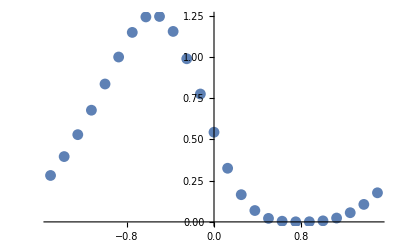

```mathematica
ListPlot[tab2]
```

```mathematica
FindMinimum[InterpolatingPolynomial[tab2,x],x]
```

{-0.000706775,{x→0.710293}}

```mathematica
FindMinimum[costFunction1[δ,{0,.1},initVals],δ]
```

initCond = {x[0]==0.1,x'[0]==10,y[0]==0.,y'[0]==1.,ψ[0]==0.,ψ'[0]==0,e_ψ[0]==0.05,e_y[0]==-1}

initCond = {x[0]==0.1,x'[0]==10,y[0]==0.,y'[0]==1.,ψ[0]==0.,ψ'[0]==0,e_ψ[0]==0.05,e_y[0]==-1}

initCond = {x[0]==0.1,x'[0]==10,y[0]==0.,y'[0]==1.,ψ[0]==0.,ψ'[0]==0,e_ψ[0]==0.05,e_y[0]==-1}

«20 more identical outputs»

$Aborted

```mathematica
NMinimize[(0.2-costFunction1[δ,{0,.1},initVals])^2,δ]
```

initCond = {x[0]==0.1,x'[0]==10,y[0]==0.,y'[0]==1.,ψ[0]==0.,ψ'[0]==0,e_ψ[0]==0.05,e_y[0]==-1}

initCond = {x[0]==0.1,x'[0]==10,y[0]==0.,y'[0]==1.,ψ[0]==0.,ψ'[0]==0,e_ψ[0]==0.05,e_y[0]==-1}

initCond = {x[0]==0.1,x'[0]==10,y[0]==0.,y'[0]==1.,ψ[0]==0.,ψ'[0]==0,e_ψ[0]==0.05,e_y[0]==-1}

«41 more identical outputs»

$Aborted

```mathematica
cf1=costFunction1[0.,{0,.1},initVals]
```

0.543616

```mathematica
ArcCos[cf1⟦2⟧-1]
```

3.0502

```mathematica
cf2=costFunction1[.258,{.1,.2},Last[cf1]]
```

initCond = {x[0.1]==1.1,x'[0.1]==10.,y[0.1]==0.0528581,y'[0.1]==0.228805,ψ[0.1]==0.0001148,ψ'[0.1]==0.00183847,e_ψ[0.1]==0.0500948,e_y[0.1]==-0.897199}

{1.32938,0.00222297,{{x→InterpolatingFunction[{{0.1, 0.2}}, <>],y→InterpolatingFunction[{{0.1, 0.2}}, <>],ψ→InterpolatingFunction[{{0.1, 0.2}}, <>],e_ψ→InterpolatingFunction[{{0.1, 0.2}}, <>],e_y→InterpolatingFunction[{{0.1, 0.2}}, <>]}},{2.08752,9.79665,0.110132,0.733231,0.0450261,0.711547,0.0949861,-0.774203}}

```mathematica
ArcCos[cf2⟦2⟧-1]
```

3.0749

```mathematica
cf3=costFunction1[-2.5,{.2,.3},Last[cf2]]
```

initCond = {x[0.2]==2.08752,x'[0.2]==9.79665,y[0.2]==0.110132,y'[0.2]==0.733231,ψ[0.2]==0.0450261,ψ'[0.2]==0.711547,e_ψ[0.2]==0.0949861,e_y[0.2]==-0.774203}

{1.22966,0.00476079,{{x→InterpolatingFunction[{{0.2, 0.3}}, <>],y→InterpolatingFunction[{{0.2, 0.3}}, <>],ψ→InterpolatingFunction[{{0.2, 0.3}}, <>],e_ψ→InterpolatingFunction[{{0.2, 0.3}}, <>],e_y→InterpolatingFunction[{{0.2, 0.3}}, <>]}},{2.99706,8.45729,0.253849,2.05884,0.188225,2.06964,0.238165,-0.493634}}

```mathematica
cf4=costFunction1[.5,{.3,.4},Last[cf3]]
```

initCond = {x[0.3]==2.99706,x'[0.3]==8.45729,y[0.3]==0.253849,y'[0.3]==2.05884,ψ[0.3]==0.188225,ψ'[0.3]==2.06964,e_ψ[0.3]==0.238165,e_y[0.3]==-0.493634}

{0.937124,0.000264641,{{x→InterpolatingFunction[{{0.3, 0.4}}, <>],y→InterpolatingFunction[{{0.3, 0.4}}, <>],ψ→InterpolatingFunction[{{0.3, 0.4}}, <>],e_ψ→InterpolatingFunction[{{0.3, 0.4}}, <>],e_y→InterpolatingFunction[{{0.3, 0.4}}, <>]}},{3.85918,8.66281,0.417715,1.43338,0.361162,1.55195,0.411082,-0.0603045}}

```mathematica
cf5=costFunction1[1.05,{.4,.5},Last[cf4]]
```

initCond = {x[0.4]==3.85918,x'[0.4]==8.66281,y[0.4]==0.417715,y'[0.4]==1.43338,ψ[0.4]==0.361162,ψ'[0.4]==1.55195,e_ψ[0.4]==0.411082,e_y[0.4]==-0.0603045}

{0.493752,0.00958245,{{x→InterpolatingFunction[{{0.4, 0.5}}, <>],y→InterpolatingFunction[{{0.4, 0.5}}, <>],ψ→InterpolatingFunction[{{0.4, 0.5}}, <>],e_ψ→InterpolatingFunction[{{0.4, 0.5}}, <>],e_y→InterpolatingFunction[{{0.4, 0.5}}, <>]}},{4.63417,6.94155,0.590082,1.99106,0.536263,1.89575,0.586163,0.456686}}

```mathematica
points={{0,0},{700/2,35},{700,40}};
plh1=InterpolatingPolynomial[points,x]//Expand
```

x/7-(3 x^2)/24500

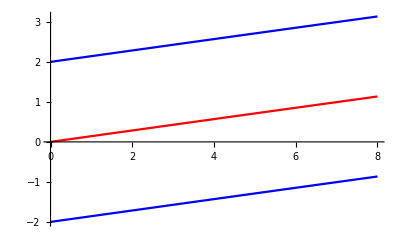

```mathematica
pl0=Plot[{plh1,plh1+2,plh1-2},{x,0,8},PlotStyle->{Red,Blue,Blue,RGBColor[0, 0.501961, 0]}]
```

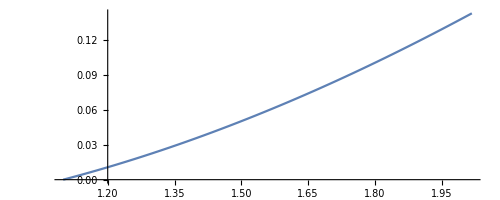

```mathematica
pl1=ParametricPlot[{x[t],y[t]}/.cf1⟦3⟧,{t,0,.10}]
```

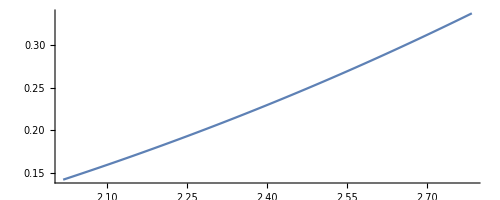

```mathematica
pl2=ParametricPlot[{x[t],y[t]}/.cf2⟦3⟧,{t,.1,.2}]
```

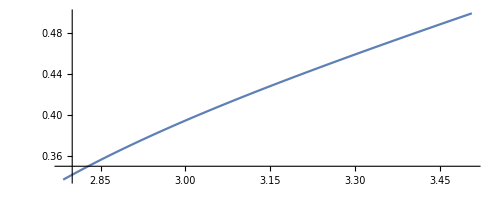

```mathematica
pl3=ParametricPlot[{x[t],y[t]}/.cf3⟦3⟧,{t,.20,.30}]
```

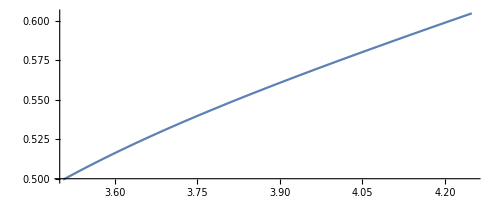

```mathematica
pl4=ParametricPlot[{x[t],y[t]}/.cf4⟦3⟧,{t,.30,.40}]
```

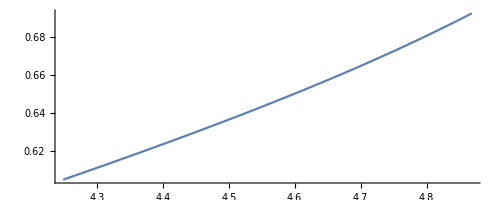

```mathematica
pl5=ParametricPlot[{x[t],y[t]}/.cf5⟦3⟧,{t,.40,.50}]
```

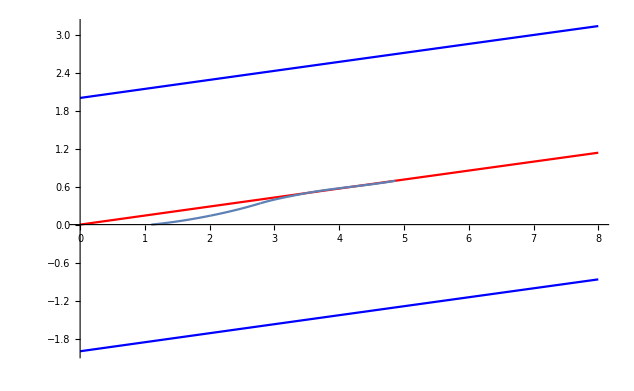

```mathematica
Show[{pl0,pl1,pl2,pl3,pl4,pl5},PlotRange->All]
```

```mathematica
tab1=ParallelTable[{δ,costFunction1[δ,{0,40},initVals]},{δ,-1.5,1.5,.025}]
```

cosθ = 0.792627

tangent = {1,0.00562167}

velocity = {0.0726163,-0.0552111}

cosθ = 0.797537

tangent = {1,0.00560941}

cosθ = 0.870865

velocity = {0.0797796,-0.0596461}

tangent = {1,0.00538195}

velocity = {0.276718,-0.154224}

cosθ = 0.802453

tangent = {1,0.00559787}

velocity = {0.0869858,-0.0639309}

cosθ = 0.875627

tangent = {1,0.00535817}

velocity = {0.302275,-0.164626}

cosθ = 0.807374

tangent = {1,0.00558652}

velocity = {0.0945128,-0.0682646}

cosθ = 0.880359

tangent = {1,0.00533272}

velocity = {0.330563,-0.175829}

cosθ = 0.812298

tangent = {1,0.00557507}

velocity = {0.102516,-0.0727452}

cosθ = 0.885057

tangent = {1,0.00530547}

velocity = {0.361909,-0.187897}

cosθ = 0.817223

tangent = {1,0.00556332}

velocity = {0.111108,-0.0774336}

cosθ = 0.889718

tangent = {1,0.00527631}

velocity = {0.396678,-0.200897}

cosθ = 0.822148

tangent = {1,0.00555112}

velocity = {0.120389,-0.0823751}

cosθ = 0.894339

tangent = {1,0.00524509}

velocity = {0.435273,-0.214896}

cosθ = 0.82707

tangent = {1,0.00553835}

velocity = {0.130456,-0.0876087}

cosθ = 0.831988

tangent = {1,0.00552491}

velocity = {0.141408,-0.0931707}

cosθ = 0.898918

tangent = {1,0.00521171}

velocity = {0.47814,-0.229961}

cosθ = 0.836898

tangent = {1,0.00551071}

velocity = {0.153356,-0.0990973}

cosθ = 0.841799

tangent = {1,0.00549564}

velocity = {0.166416,-0.105426}

cosθ = 0.903451

tangent = {1,0.00517603}

velocity = {0.52577,-0.246154}

cosθ = 0.846688

tangent = {1,0.00547963}

velocity = {0.180721,-0.112195}

cosθ = 0.907936

tangent = {1,0.00513791}

velocity = {0.578695,-0.263532}

cosθ = 0.851563

tangent = {1,0.00546257}

velocity = {0.196418,-0.119447}

cosθ = 0.912368

tangent = {1,0.00509726}

velocity = {0.637486,-0.282139}

cosθ = 0.85642

tangent = {1,0.00544437}

velocity = {0.21367,-0.127227}

cosθ = 0.916746

tangent = {1,0.00505394}

velocity = {0.702749,-0.302005}

cosθ = 0.861258

tangent = {1,0.00542494}

velocity = {0.232662,-0.135581}

cosθ = 0.921066

tangent = {1,0.00500786}

velocity = {0.775117,-0.323137}

cosθ = 0.866074

tangent = {1,0.00540417}

velocity = {0.253601,-0.144562}

cosθ = 0.925325

tangent = {1,0.00495894}

velocity = {0.85523,-0.34551}

cosθ = 0.937701

tangent = {1,0.0047946}

velocity = {1.14821,-0.419193}

cosθ = 0.929519

tangent = {1,0.00490712}

velocity = {0.943725,-0.369061}

cosθ = 0.94168

tangent = {1,0.00473391}

velocity = {1.26519,-0.445374}

cosθ = 0.933646

tangent = {1,0.00485234}

velocity = {1.0412,-0.393678}

cosθ = 0.986061

tangent = {1,0.00360812}

velocity = {3.92192,-0.647215}

cosθ = 0.945579

tangent = {1,0.00467032}

velocity = {1.39249,-0.471919}

cosθ = 0.988159

tangent = {1,0.003505}

velocity = {4.18562,-0.634896}

cosθ = 0.949393

tangent = {1,0.0046039}

cosθ = 0.990088

velocity = {1.53027,-0.498457}

tangent = {1,0.00339663}

velocity = {4.46605,-0.618068}

cosθ = 0.953117

tangent = {1,0.00453474}

velocity = {1.67855,-0.524554}

cosθ = 0.956743

tangent = {1,0.00446295}

velocity = {1.83717,-0.549721}

cosθ = 0.991846

tangent = {1,0.00328213}

velocity = {4.76725,-0.596641}

cosθ = 0.960264

tangent = {1,0.00438866}

velocity = {2.00582,-0.573438}

cosθ = 0.963675

tangent = {1,0.00431195}

velocity = {2.18404,-0.595171}

cosθ = 0.993432

tangent = {1,0.00316048}

velocity = {5.09439,-0.570461}

cosθ = 0.994844

tangent = {1,0.00303064}

velocity = {5.45387,-0.539272}

cosθ = 0.966966

tangent = {1,0.00423291}

velocity = {2.37136,-0.614402}

cosθ = 0.996081

tangent = {1,0.00289161}

velocity = {5.85344,-0.502685}

cosθ = 0.97013

tangent = {1,0.00415158}

velocity = {2.56727,-0.630649}

cosθ = 0.997141

tangent = {1,0.00274269}

velocity = {6.302,-0.460163}

cosθ = 0.973159

tangent = {1,0.00406793}

velocity = {2.77142,-0.643492}

cosθ = 0.998024

tangent = {1,0.00258387}

velocity = {6.8087,-0.411044}

cosθ = 0.998728

tangent = {1,0.00241664}

velocity = {7.38028,-0.354689}

cosθ = 0.976047

tangent = {1,0.00398187}

velocity = {2.98361,-0.652586}

cosθ = 0.999258

tangent = {1,0.00224531}

velocity = {8.01457,-0.290851}

cosθ = 0.978786

tangent = {1,0.0038932}

velocity = {3.20397,-0.657663}

cosθ = 0.999623

tangent = {1,0.00207903}

velocity = {8.687,-0.220416}

cosθ = 0.999845

tangent = {1,0.00193379}

velocity = {9.32924,-0.14617}

cosθ = 0.981371

tangent = {1,0.00380164}

velocity = {3.43304,-0.658534}

cosθ = 0.999958

tangent = {1,0.00183189}

velocity = {9.81556,-0.0721264}

cosθ = 0.983798

tangent = {1,0.00370679}

velocity = {3.67182,-0.655077}

cosθ = 0.999985

tangent = {1,0.00183189}

velocity = {9.81556,0.0721264}

cosθ = 0.999998

tangent = {1,0.00179494}

velocity = {10.,4.38561×10^-16}

cosθ = 0.999906

tangent = {1,0.00193379}

velocity = {9.32924,0.14617}

cosθ = 0.999729

tangent = {1,0.00207903}

velocity = {8.687,0.220416}

cosθ = 0.999421

tangent = {1,0.00224531}

velocity = {8.01457,0.290851}

cosθ = 0.99896

tangent = {1,0.00241664}

velocity = {7.38028,0.354689}

cosθ = 0.982804

tangent = {1,0.00380164}

velocity = {3.43304,0.658534}

cosθ = 0.998335

tangent = {1,0.00258387}

velocity = {6.8087,0.411044}

cosθ = 0.980352

tangent = {1,0.0038932}

velocity = {3.20397,0.657663}

cosθ = 0.997541

tangent = {1,0.00274269}

velocity = {6.302,0.460163}

cosθ = 0.996576

tangent = {1,0.00289161}

velocity = {5.85344,0.502685}

cosθ = 0.995441

tangent = {1,0.00303064}

velocity = {5.45387,0.539272}

cosθ = 0.977748

tangent = {1,0.00398187}

velocity = {2.98361,0.652586}

cosθ = 0.994136

tangent = {1,0.00316048}

velocity = {5.09439,0.570461}

cosθ = 0.992661

tangent = {1,0.00328213}

velocity = {4.76725,0.596641}

cosθ = 0.974999

tangent = {1,0.00406793}

velocity = {2.77142,0.643492}

cosθ = 0.991019

tangent = {1,0.00339663}

velocity = {4.46605,0.618068}

cosθ = 0.98921

tangent = {1,0.003505}

velocity = {4.18562,0.634896}

cosθ = 0.972111

tangent = {1,0.00415158}

velocity = {2.56727,0.630649}

cosθ = 0.969089

tangent = {1,0.00423291}

velocity = {2.37136,0.614402}

cosθ = 0.987236

tangent = {1,0.00360812}

velocity = {3.92192,0.647215}

cosθ = 0.9851

tangent = {1,0.00370679}

velocity = {3.67182,0.655077}

cosθ = 0.965942

tangent = {1,0.00431195}

velocity = {2.18404,0.595171}

cosθ = 0.933093

tangent = {1,0.00490712}

velocity = {0.943725,0.369061}

cosθ = 0.962677

tangent = {1,0.00438866}

velocity = {2.00582,0.573438}

cosθ = 0.92904

tangent = {1,0.00495894}

velocity = {0.85523,0.34551}

cosθ = 0.959301

tangent = {1,0.00446295}

velocity = {1.83717,0.549721}

cosθ = 0.92492

tangent = {1,0.00500786}

velocity = {0.775117,0.323137}

cosθ = 0.955822

tangent = {1,0.00453474}

velocity = {1.67855,0.524554}

cosθ = 0.920737

tangent = {1,0.00505394}

velocity = {0.702749,0.302005}

cosθ = 0.952245

tangent = {1,0.0046039}

velocity = {1.53027,0.498457}

cosθ = 0.916494

tangent = {1,0.00509726}

velocity = {0.637486,0.282139}

cosθ = 0.948577

cosθ = 0.912194

tangent = {1,0.00467032}

tangent = {1,0.00513791}

velocity = {1.39249,0.471919}

velocity = {0.578695,0.263532}

cosθ = 0.944824

tangent = {1,0.00473391}

velocity = {1.26519,0.445374}

cosθ = 0.90784

tangent = {1,0.00517603}

velocity = {0.52577,0.246154}

cosθ = 0.940989

tangent = {1,0.0047946}

velocity = {1.14821,0.419193}

cosθ = 0.903436

tangent = {1,0.00521171}

velocity = {0.47814,0.229961}

cosθ = 0.937078

tangent = {1,0.00485234}

velocity = {1.0412,0.393678}

cosθ = 0.898983

tangent = {1,0.00524509}

velocity = {0.435273,0.214896}

cosθ = 0.866721

tangent = {1,0.00542494}

velocity = {0.232662,0.135581}

cosθ = 0.894486

tangent = {1,0.00527631}

velocity = {0.396678,0.200897}

cosθ = 0.861991

tangent = {1,0.00544437}

velocity = {0.21367,0.127227}

cosθ = 0.889946

tangent = {1,0.00530547}

velocity = {0.361909,0.187897}

cosθ = 0.857239

tangent = {1,0.00546257}

velocity = {0.196418,0.119447}

cosθ = 0.885367

tangent = {1,0.00533272}

velocity = {0.330563,0.175829}

cosθ = 0.880753

cosθ = 0.852469

tangent = {1,0.00535817}

tangent = {1,0.00547963}

velocity = {0.302275,0.164626}

velocity = {0.180721,0.112195}

cosθ = 0.876105

tangent = {1,0.00538195}

velocity = {0.276718,0.154224}

cosθ = 0.847681

tangent = {1,0.00549564}

velocity = {0.166416,0.105426}

cosθ = 0.871427

tangent = {1,0.00540417}

velocity = {0.253601,0.144562}

cosθ = 0.84288

tangent = {1,0.00551071}

velocity = {0.153356,0.0990973}

cosθ = 0.838067

tangent = {1,0.00552491}

velocity = {0.141408,0.0931707}

cosθ = 0.833246

tangent = {1,0.00553835}

velocity = {0.130456,0.0876087}

cosθ = 0.828418

tangent = {1,0.00555112}

velocity = {0.120389,0.0823752}

cosθ = 0.823585

tangent = {1,0.00556332}

velocity = {0.111108,0.0774336}

cosθ = 0.81875

tangent = {1,0.00557507}

velocity = {0.102516,0.0727452}

cosθ = 0.813915

tangent = {1,0.00558652}

velocity = {0.0945128,0.0682646}

cosθ = 0.809083

tangent = {1,0.00559787}

velocity = {0.0869858,0.0639309}

cosθ = 0.804254

tangent = {1,0.00560941}

velocity = {0.0797796,0.0596461}

cosθ = 0.799432

tangent = {1,0.00562167}

velocity = {0.0726163,0.0552111}

{{-1.5,{656.394,0.207373}},{-1.475,{727.481,0.202463}},{-1.45,{788.156,0.197547}},{-1.425,{842.825,0.192626}},{-1.4,{893.752,0.187702}},{-1.375,{942.251,0.182777}},{-1.35,{989.149,0.177852}},{-1.325,{1035.,0.17293}},{-1.3,{1080.2,0.168012}},{-1.275,{1125.02,0.163102}},{-1.25,{1169.68,0.158201}},{-1.225,{1214.34,0.153312}},{-1.2,{1259.12,0.148437}},{-1.175,{1304.11,0.14358}},{-1.15,{1349.38,0.138742}},{-1.125,{1394.98,0.133926}},{-1.1,{1440.94,0.129135}},{-1.075,{1487.26,0.124373}},{-1.05,{1533.95,0.119641}},{-1.025,{1580.98,0.114943}},{-1.,{1628.32,0.110282}},{-0.975,{1675.89,0.105661}},{-0.95,{1723.62,0.101082}},{-0.925,{1771.4,0.0965488}},{-0.9,{1819.1,0.0920645}},{-0.875,{1866.56,0.0876319}},{-0.85,{1913.58,0.0832541}},{-0.825,{1959.95,0.0789342}},{-0.8,{2005.39,0.0746754}},{-0.775,{2049.62,0.070481}},{-0.75,{2092.3,0.0663544}},{-0.725,{2133.07,0.0622994}},{-0.7,{2171.53,0.0583199}},{-0.675,{2207.26,0.0544206}},{-0.65,{2239.85,0.0506066}},{-0.625,{2268.85,0.0468834}},{-0.6,{2293.85,0.0432575}},{-0.575,{2314.43,0.0397357}},{-0.55,{2330.22,0.0363254}},{-0.525,{2340.88,0.0330343}},{-0.5,{2346.13,0.0298703}},{-0.475,{2345.71,0.0268408}},{-0.45,{2339.41,0.0239532}},{-0.425,{2327.04,0.0212139}},{-0.4,{2308.43,0.0186286}},{-0.375,{2283.39,0.0162022}},{-0.35,{2251.71,0.0139386}},{-0.325,{2213.12,0.0118411}},{-0.3,{2167.24,0.00991218}},{-0.275,{2113.56,0.00815388}},{-0.25,{2051.39,0.00656789}},{-0.225,{1979.78,0.00515573}},{-0.2,{1897.45,0.00391887}},{-0.175,{1802.71,0.00285872}},{-0.15,{1693.32,0.00197637}},{-0.125,{1566.38,0.00127176}},{-0.1,{1418.17,0.000741793}},{-0.075,{1243.77,0.000376635}},{-0.05,{1035.4,0.000154885}},{-0.025,{775.469,0.0000421352}},{1.52656×10^-16,{400.103,1.6109×10^-6}},{0.025,{529.859+0. ⅈ,0.0000152139}},{0.05,{937.12+0. ⅈ,0.0000942951}},{0.075,{1218.34+0. ⅈ,0.000271167}},{0.1,{1444.21+0. ⅈ,0.000578934}},{0.125,{1633.23+0. ⅈ,0.00103975}},{0.15,{1794.18+0. ⅈ,0.00166496}},{0.175,{1932.69+0. ⅈ,0.00245925}},{0.2,{2052.82+0. ⅈ,0.00342404}},{0.225,{2157.59+0. ⅈ,0.00455931}},{0.25,{2249.28+0. ⅈ,0.00586448}},{0.275,{2329.62+0. ⅈ,0.0073387}},{0.3,{2399.89+0. ⅈ,0.00898092}},{0.325,{2461.06+0. ⅈ,0.0107898}},{0.35,{2513.85+0. ⅈ,0.0127636}},{0.375,{2558.8+0. ⅈ,0.0149001}},{0.4,{2596.33+0. ⅈ,0.0171962}},{0.425,{2626.75+0. ⅈ,0.0196482}},{0.45,{2650.33+0. ⅈ,0.0222516}},{0.475,{2667.31+0. ⅈ,0.0250007}},{0.5,{2677.92+0. ⅈ,0.0278895}},{0.525,{2682.41+0. ⅈ,0.030911}},{0.55,{2681.03+0. ⅈ,0.034058}},{0.575,{2674.11+0. ⅈ,0.037323}},{0.6,{2661.97+0. ⅈ,0.0406988}},{0.625,{2644.99+0. ⅈ,0.0441782}},{0.65,{2623.58+0. ⅈ,0.0477548}},{0.675,{2598.16+0. ⅈ,0.0514226}},{0.7,{2569.15+0. ⅈ,0.0551762}},{0.725,{2536.98+0. ⅈ,0.0590108}},{0.75,{2502.08+0. ⅈ,0.0629223}},{0.775,{2464.84+0. ⅈ,0.0669066}},{0.8,{2425.63+0. ⅈ,0.0709604}},{0.825,{2384.79+0. ⅈ,0.0750803}},{0.85,{2342.62+0. ⅈ,0.0792632}},{0.875,{2299.41+0. ⅈ,0.0835061}},{0.9,{2255.38+0. ⅈ,0.0878058}},{0.925,{2210.76+0. ⅈ,0.0921595}},{0.95,{2165.7+0. ⅈ,0.0965642}},{0.975,{2120.35+0. ⅈ,0.101017}},{1.,{2074.85+0. ⅈ,0.105514}},{1.025,{2029.28+0. ⅈ,0.110054}},{1.05,{1983.71+0. ⅈ,0.114633}},{1.075,{1938.2+0. ⅈ,0.119247}},{1.1,{1892.78+0. ⅈ,0.123895}},{1.125,{1847.47+0. ⅈ,0.128573}},{1.15,{1802.25+0. ⅈ,0.133279}},{1.175,{1757.11+0. ⅈ,0.138009}},{1.2,{1711.99+0. ⅈ,0.142761}},{1.225,{1666.83+0. ⅈ,0.147531}},{1.25,{1621.54+0. ⅈ,0.152319}},{1.275,{1575.98+0. ⅈ,0.15712}},{1.3,{1529.98+0. ⅈ,0.161933}},{1.325,{1483.31+0. ⅈ,0.166754}},{1.35,{1435.65+0. ⅈ,0.171582}},{1.375,{1386.56+0. ⅈ,0.176415}},{1.4,{1335.4+0. ⅈ,0.18125}},{1.425,{1281.22+0. ⅈ,0.186085}},{1.45,{1222.49+0. ⅈ,0.190917}},{1.475,{1156.54+0. ⅈ,0.195746}},{1.5,{1078.11+0. ⅈ,0.200568}}}

```mathematica
tab2=Map[({{First[#],First[Last[#]]},{First[#],Last[Last[#]]}})&,tab1];
```

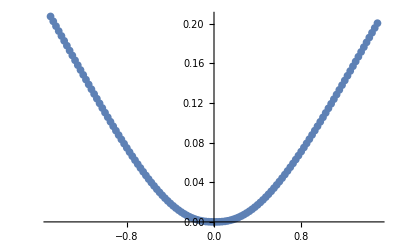

```mathematica
ListPlot[Last[Transpose[tab2]]]
```

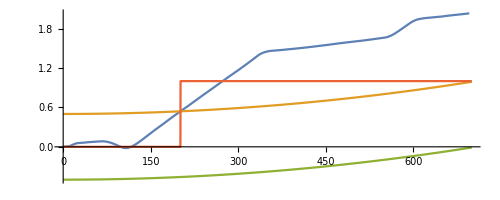

```mathematica
scale =10;
P1 = ParametricPlot[{{x[t],y[t]}/.solution,{scale *t,u[t]},{scale *t, u[t]-1},{scale *t,FlagY/.solution}(*{10t, Subscript[e, y][t]/.solution}{t,Sqrt[(x[t])^2+(y[t])^2]/.solution}*)},{t,0,time},AspectRatio->Full,PlotRange->All]
```

```mathematica
FlagY =Piecewise[{{0, u[t]>y[t] > u[t]-1}, {1, True}}];
Subscript[Flag, ey] =Piecewise[{{1, Subscript[e, y][t] > 200}, {0, Subscript[e, y][t]≤  200}}];
Subscript[Flag, slip1] =Piecewise[{{0, 0.07>α1 > -0.07}, {1, True}}];
Subscript[Flag, slip2] =Piecewise[{{0, 0.07>Subscript[α, 2] > -0.07}, {1, True}}];
Subscript[Flag, slip3] =Piecewise[{{0, 0.07>Subscript[α, 3] > -0.07}, {1, True}}];
Subscript[Flag, slip4]=Piecewise[{{0, 0.07>Subscript[α, 4] > -0.07}, {1, True}}];
```

```mathematica
f5[x_,y_,l2_,s1_,s2_]:=Plot[Evaluate[{x,y}/.solution],{t,0,time},Frame->True,FrameLabel->{sec,l2},PlotLegends->{s1,s2},PlotRange->All] ;
f5[x[t],y[t],m,x[t],"y(t)"];
f5[x'[t],y'[t],"km/h","v_x(t)","v_y(t)"]
f5[x''[t],y''[t],"m/s^2","a_x(t)","a_y(t)"];
f5[δ,,"deg","δ",""]
f5[ψ'[t],,"","ψ'[t]",""]
f5[u[t],,"","Angle of tangent to road centerline",""]
Plot1 = ParametricPlot[{{x[t],y[t]}/.solution},{t,0,time},PlotRange-> All,AspectRatio->Full];
Plot2 = ParametricPlot[{{u[t]}},{t,0,time},PlotRange-> All];
Show[{Plot1,Plot2}, PlotRange-> All];
f5[α1*180/π,,"rad","α1",""]
f5[Subscript[e, ψ]'[t]/.solution,,"rad","e_ψ'",""]
f5[Subscript[e, ψ][t]/.solution,,"rad","e_ψ",""]

f5[Subscript[Flag, ey],,"-","Flag_ey",""];
f5[u[t],,"","psid",""];
Plot[Evaluate[{Subscript[Flag, slip1],Subscript[Flag, slip2],Subscript[Flag, slip3],Subscript[Flag, slip4]}/.solution],{t,0,time},Frame->True,FrameLabel->{sec,""},PlotLegends->{"Flag_slip1","Flag_slip2","Flag_slip3","Flag_slip4"},PlotRange->All] ;

(* The upper parabola is the left boundary of the road. The mid parabola is the center of the road. The bottom parabola is the lower bound of the road. There isa flag FlagY tetecting the crossing of the mid of the road. Your flag Subscript[Flag, ey] detects a value of ey[t]. The road is represented using time as parameter. This needs the knowledge of the maximal value of the elongation x as a function of t (here about 700). To match the scales there must be a reduction of x by a factor 10 or an amplification of the x-coordinate of the road by 10 which is used here. The y coordinate of the road uses a scaled version of your curve using C1 and C0 *)
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

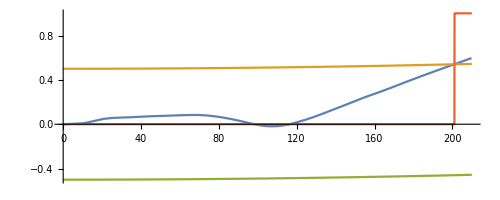

```mathematica
scale =10;
P1 = ParametricPlot[{{x[t],y[t]}/.solution,{scale *t,u[t]},{scale *t, u[t]-1},{scale *t,FlagY/.solution}(*{10t, Subscript[e, y][t]/.solution}{t,Sqrt[(x[t])^2+(y[t])^2]/.solution}*)},{t,0,21},AspectRatio->Full,PlotRange->All]
```

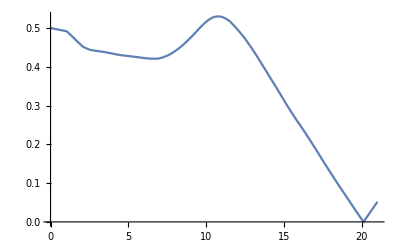

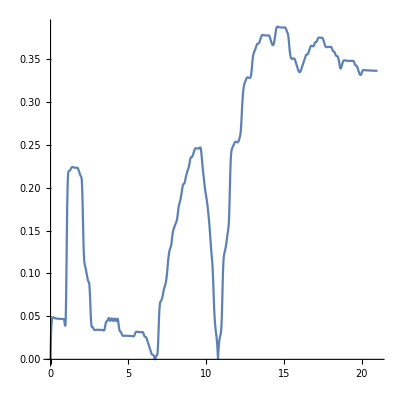

```mathematica
dx = 0;
dy = y[t] - u[t];
dc = {dx,dy};
ce = Sqrt[dc.dc];
Plot[ce/.solution,{t,0,21}]
road= {11,D[u[t],t]};
vel = {x'[t],y'[t]};
k = (road.vel)/(Norm[road]*Norm[vel]);
Plot[ArcCos[k]*180/π/.solution,{t,0,21},AspectRatio->1,PlotRange->All]
```

## Road Model in the Simulation

The idea is to estimate the extension of the motion in x and y direction. So we estimate the maximal extension of the road as (x_min,x_max)×(y_min,y_max) where the extremal values determine the range of a rectangle. Within this range we define the road and the ideal line as an interpolation polynomial as follows. x_min and y_min can be choosen in the origin without any restrictions. If we like to generate a 2^nd order polynomial for the ideal line we need 3 interpolation points which one of them is the origin

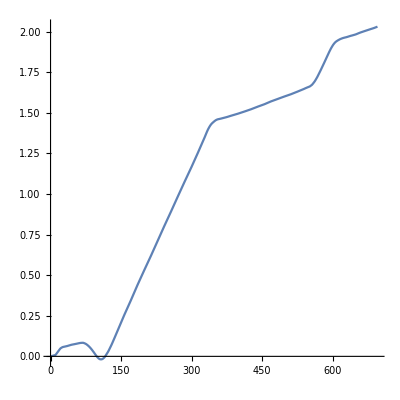

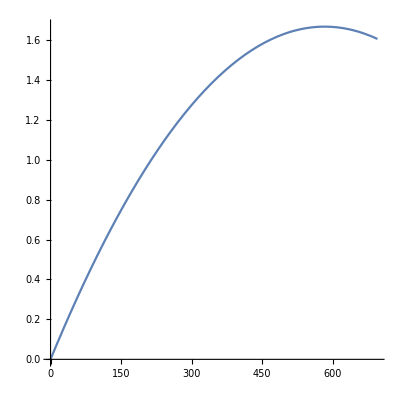

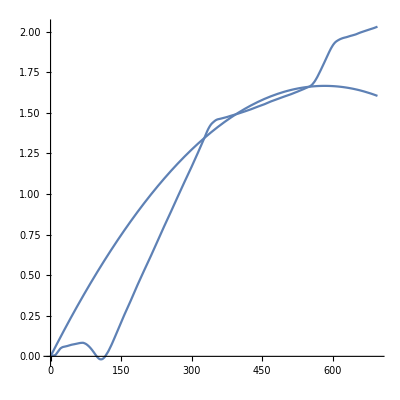

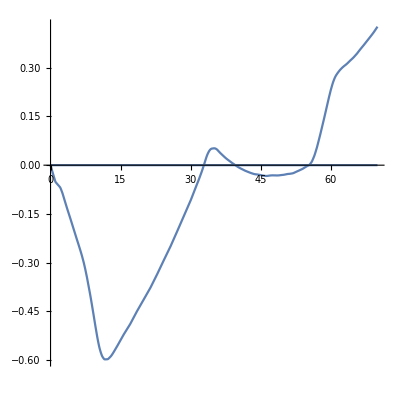

```mathematica
points={{0,0},{700/2,35},{700,40}};
pl1=InterpolatingPolynomial[points,x]/25//Expand;
x1 = ParametricPlot[{x[t],y[t]}/.solution,{t,0,time},AspectRatio->1]
x2 = ParametricPlot[{x[t],pl1/.x-> x[t]}/.solution,{t,0,time},AspectRatio->1]
Show[x1,x2]
ΔxVec={0,-(pl1/.x->x[t])+y[t]};
lineElement=ΔxVec;
x3 = Plot[lineElement/.solution,{t,0,time},AspectRatio->1,PlotRange->Full]
```

```mathematica
tangentVec={1,D[pl1,x]}/.x->x[t]
```

{1,1/175-(3 x[t])/306250}

The velocity is derived from the trajectory of the car as

```mathematica
velocity={x'[t],y'[t]}
```

{x'[t],y'[t]}

The allignement along the ideal track is found by the relation |cos(θ)|=1 which is equivalent to 1=|(t⃗.v⃗)/(|t⃗| |v⃗|)| which is implemented next as difference

```mathematica
ori =  (velocity.tangentVec)/(Norm[velocity] Norm[tangentVec]);
allignment=1-Abs[(velocity.tangentVec)/(Norm[velocity] Norm[tangentVec])];
```

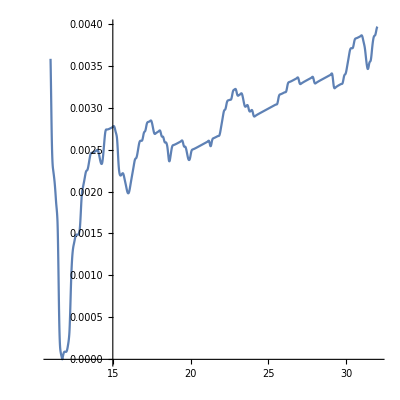

```mathematica
Plot[ArcCos[ori]/.solution,{t,11,32},AspectRatio->1,PlotRange->Full]
```

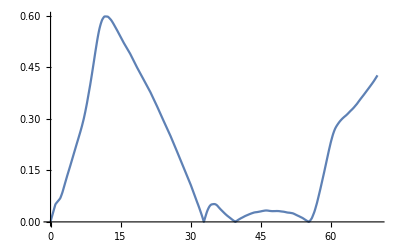

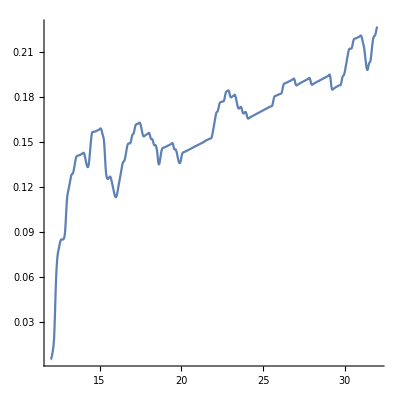

```mathematica
dx = 0;
dy = y[t] - pl1/.x->x[t];
dc = {dx,dy};
ce = Sqrt[dc.dc];
Plot[ce/.solution,{t,0,time}]
road= {1,D[pl1,x]/.x->x[t]};
vel = {x'[t],y'[t]};
k = (road.vel)/(Norm[road]*Norm[vel]);
Plot[ArcCos[k]*180/π/.solution,{t,12,32},AspectRatio->1,PlotRange->All]
```

Finally we need the reference velocity lets call it v_Max which we compare with the current velocity v of the car

```mathematica
ΔVelocity=vMax-Norm[{x'[t],y'[t]}]
```

vMax-√(Abs[x'[t]]^2+Abs[y'[t]]^2)

The cost function can now be written as

```mathematica
kostFunction=α lineElement^2/.{α->1/3}
```

1/3 Abs[x[t]/175-(3 x[t]^2)/612500-y[t]]^2

with α, β, and γ as weights of the function. This implementation should be completely independent of the scaling of the previously used parametric representation of the road.

## How to use the CostFunction

First define the cost function generating the results and using the unspecified parameters in the following example a. I solve a differential equation on a fixed time domain and like to find the value for the parameter a which minimizes my result with respect to a given value for a; e.g. a=2.

This function defines the partial costfunction

```mathematica
f[a_?NumericQ]:=Block[{solution,x,y,ψ,δ},
solution=Flatten[NDSolve[{motionEq,initCond},δ,{x,0,700}]];
vv=(kostFunction=α lineElement^2/.{α->1/3})
]
```

If I use the function with a symbolic argument nothing happens. The definition assumes that a is numeric which is important in the optimization

```mathematica
f[a]
```

f[a]

The cost function I’m interest in is (2-f(a))^2. The following table shows that ther is a minimal value.

```mathematica
Table[(-f[a])^2/.solution,{a,0,5,.1}]
```

NDSolve::ivhead: The independent variable x appears in the head of the expression x[0]. The independent variables should always be arguments.

General::stop: Further output of NDSolve :: ivhead will be suppressed during this calculation.

{{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4},{1/9 Abs[-InterpolatingFunction[{{0., 70.}}, <>][t]+1/175 InterpolatingFunction[{{0., 70.}}, <>][t]-(3 (InterpolatingFunction[{{0., 70.}}, <>][t])^2)/612500]^4}}

The graph represents the same fact

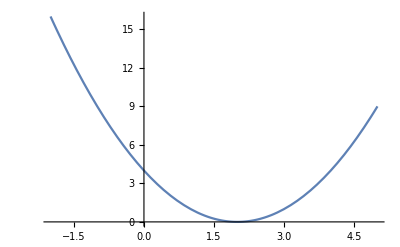

```mathematica
Plot[(2-f[a])^2,{a,-2,5}]
```

Now using FindMinimum allows me to get the minimal value for a which is near by the assumed value

```mathematica
min=FindMinimum[(2-f[a])^2,a]
```

{4.93038×10^-32,{a→2.00014}}

With the optimal solution given by

```mathematica
solution=Flatten[NDSolve[{D[y[x], x]==-y[x]+a/.Last[min],y[0]==-1},y,{x,0,10}]]
```

{y→InterpolatingFunction[{{0., 10.}}, <>]}

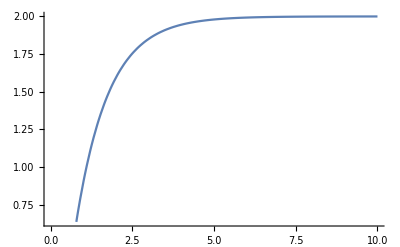

```mathematica
Plot[y[x]/.solution,{x,0,10}]
```